### QW inflection

```mathematica
Integrate[Sin[(3π)/2 x]^2,{x,0,1}]
```

1/2

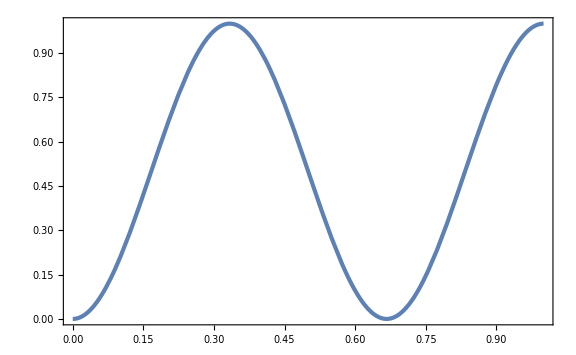

```mathematica
Plot[Sin[(1+1/2)π x]^2,{x,0,1}]
```

```mathematica
normN=Integrate[Exp[(-(x-1)^2)/σ^2],{x,0,1}]^(-1/2)
```

(√2)/(π^(1/4) √(σ Erf[1/σ]))

```mathematica
Integrate[(normN Exp[(-(x-1)^2)/(2 σ^2)])^2,{x,0,1}]
```

1

```mathematica
αn[n_]= Integrate[normN Exp[(-(x-1)^2)/(2 σ^2)]Sqrt[2]Sin[(n+1/2)π x],{x,0,1}]//Simplify
```

-(ⅈ ⅇ^(-1/8 π (8 ⅈ n+π (σ+2 n σ)^2)) π^(1/4) σ ((-1+ⅇ^(2 ⅈ n π)) Erfi[((1+2 n) π σ)/(2 √2)]-ⅇ^(2 ⅈ n π) Erfi[(-2 ⅈ+(1+2 n) π σ^2)/(2 √2 σ)]+Erfi[(2 ⅈ+(1+2 n) π σ^2)/(2 √2 σ)]))/(√2 √(σ Erf[1/σ]))

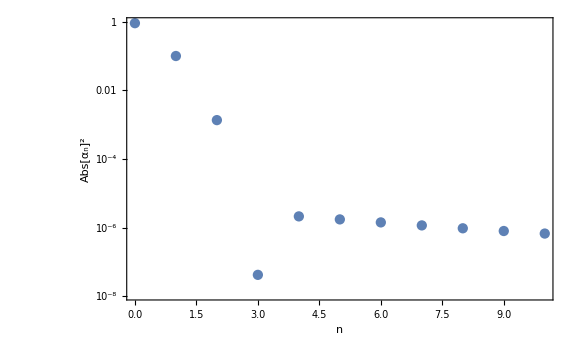

```mathematica
ListLogPlot[Table[{n,Abs[N[αn[n]/.{σ->1/3},30]]^2},{n,0,10}],Joined->False,FrameLabel->{n,Abs[Subscript[α, n]]^2}]
```

### QW hilltop

```mathematica
Integrate[Sin[2π x]^2,{x,0,1}]
```

1/2

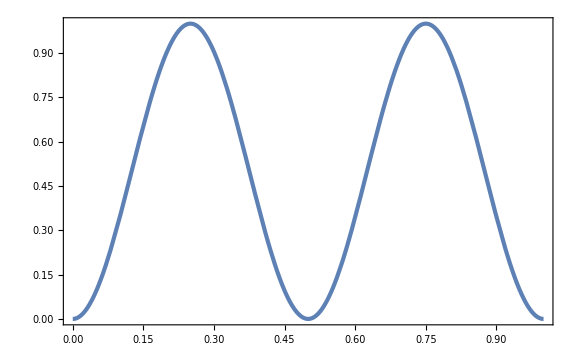

```mathematica
Plot[Sin[2π x]^2,{x,0,1}]
```

```mathematica
Integrate[Exp[(-(x-1/2)^2)/σ^2],{x,0,1}]
```

√π σ Erf[1/(2 σ)]

```mathematica
normN=Integrate[Exp[(-(x-1/2)^2)/σ^2],{x,0,1}]^(-1/2)
```

1/(π^(1/4) √(σ Erf[1/(2 σ)]))

```mathematica
Integrate[(normN Exp[(-(x-1/2)^2)/(2 σ^2)])^2,{x,0,1}]
```

1

```mathematica
αn[n_]= Integrate[normN Exp[(-(x-1/2)^2)/(2 σ^2)]Sqrt[2]Sin[n π x],{x,0,1}]//Simplify
```

(ⅇ^(-1/2 n π (ⅈ+n π σ^2)) (-1+ⅇ^(ⅈ n π)) π^(1/4) σ (Erfi[(-ⅈ+2 n π σ^2)/(2 √2 σ)]-Erfi[(ⅈ+2 n π σ^2)/(2 √2 σ)]))/(2 √(σ Erf[1/(2 σ)]))

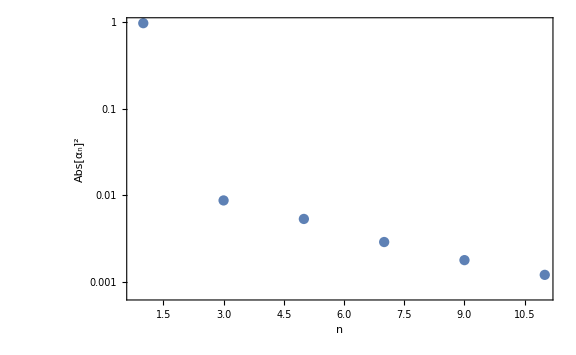

```mathematica
ListLogPlot[Table[{n,Abs[N[αn[n]/.{σ->1/3},30]]^2},{n,1,11}],Joined->False,FrameLabel->{n,Abs[Subscript[α, n]]^2},PlotRange->Full]
```

### Hilltop

```mathematica
w[x_]=E^(1/v[x])/v[x];
LFPF=Collect[w[x]^(1/2)((-v'[x])/v[x] D[(w[x]^(-1/2)F[x]), x]+v[x]D[D[(w[x]^(-1/2)F[x]), x], x])//Simplify,{F[x],F'[x],F''[x]},Simplify]
```

F'[x] v'[x]+v[x] F''[x]+(F[x] (-((1+4 v[x]+v[x]^2) v'[x]^2)+2 v[x]^2 (1+v[x]) v''[x]))/(4 v[x]^3)

```mathematica
Collect[w[x]^(-1/2)(D[(v'[x]/v[x] w[x]^(1/2)F[x]), x]+D[D[(v[x] w[x]^(1/2)F[x]), x], x])//Simplify,{F[x],F'[x],F''[x]},Simplify]
```

F'[x] v'[x]+v[x] F''[x]+(F[x] (-((1+4 v[x]+v[x]^2) v'[x]^2)+2 v[x]^2 (1+v[x]) v''[x]))/(4 v[x]^3)

```mathematica
(D[(v'[x]/v[x] w[x]F[x]), x]+D[D[(v[x]w[x]F[x]), x], x])/w[x]//Simplify
```

-(F'[x] v'[x])/v[x]+v[x] F''[x]

```mathematica
vh[x_]=v0(1-λ x^p)^2;
```

```mathematica
LFPFhill=Collect[Normal[Series[LFPF/.{v[x]->v0,v'[x]->vh'[x],v''[x]->vh''[x]},{λ,0,1}]],{F[x],F'[x],F''[x]},Simplify]
```

-((-1+p) p (1+v0) x^(-2+p) λ F[x])-2 p v0 x^(-1+p) λ F'[x]+v0 F''[x]

```mathematica
DSolve[LFPFhill==-Λn F[x]/.{p->2},F[x],x]//Simplify
```

{{F[x]→C[1] HermiteH[(-2 (1+v0) λ+Λn)/(4 v0 λ),√2 x √λ]+C[2] Hypergeometric1F1[-(-2 (1+v0) λ+Λn)/(8 v0 λ),1/2,2 x^2 λ]}}

```mathematica
DSolve[LFPFhill==-Λn F[x]/.{p->4}//Simplify,F[x],x]
```

{{F[x]→[x]}}